# Unidad 2 1- Ecuaciones diferenciales y sistemas caóticos

## Ecuación diferencial simple con solución analítica

Una ecuación diferencial se puede resolver analíicamente en Mathematica.

```mathematica
DSolve[x'[t] == k x[t],{x},t]
```

{{x→Function[{t},ⅇ^(k t) C[1]]}}

Se pueden especificar las condiciones iniciales.

```mathematica
sol = First[DSolve[{x'[t] == k x[t](c- x[t]),x[0]==P0},{x},t]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{x→Function[{t},(c ⅇ^(c k t) P0)/(c-P0+ⅇ^(c k t) P0)]}

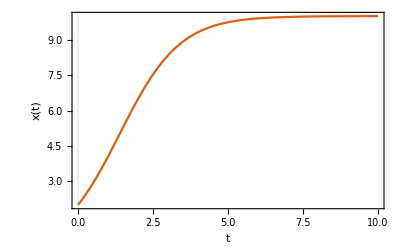

```mathematica
Plot[(x[t] /. sol) /. {P0->2,c->10, k-> 0.1},{t,0,10},PlotTheme->"Scientific", FrameLabel->{"t", "x(t)"},BaseStyle->FontSize->14]
```

## Resolver una ecuación diferencial simple (numéricamente)

El péndulo simple cuya ecuación de movimiento es θ’’[t] + g/l sen(θ(t)) = 0.

```mathematica
g = 9.8;
l=1;
sol1 = NDSolve[{θ''[t] +g/l Sin[θ[t]] == 0,θ[0] ==1,θ'[0]==0},{θ},{t,0,5}];
sol2 = NDSolve[{θ''[t] +g/l θ[t] == 0,θ[0] ==1,θ'[0]==0},{θ},{t,0,5}];
```

```mathematica
Plot[{θ[t]/. sol1,θ[t]/. sol2},{t,0,5}]
```

```mathematica
DSolve[{θ''[t] +g/l θ[t] == 0,θ[0] ==1,θ'[0]==0},{θ},t]
```

Para la visualización del espacio de fase se hace

```mathematica
ParametricPlot[{θ[t],θ'[t]} /. sol1,{t,0,5},AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{"θ(t)","θ'(t)"},BaseStyle->FontSize->14]
```

Si queremos visualizar el espacio de fase para diferentes condiciones iniciales (de velocidad)

```mathematica
g = 9.8;
l=1;
soluciones = Table[NDSolve[{θ''[t] +g/l Sin[θ[t]] == 0,θ[0] ==0,θ'[0]==ω},{θ},{t,0,5}],{ω,1,7}];
ParametricPlot[{θ[t],θ'[t]} /.soluciones,{t,0,5},AspectRatio->1,PlotTheme->"Scientific",FrameLabel->{"θ(t)","θ'(t)"},BaseStyle->FontSize->14]
```

## Solución numérica del doble péndulo

El doble péndulo es un ejemplo de sistema mecánico que pone en evidencia la complejidad que pueden generar este tipo de sistemas de construcción simple. Este sistema en su forma más simple está formado por dos masas colgando de cuerdas de masa despreciable y sin fricción, donde las masas están sujetas a la acción de la gravedad. Se desea describir el movimiento de ambas masas.

No es posible obtener la solución en términos de funciones elementales para este par de ecuaciones diferenciales, lo que pone en evidencia la naturaleza caótica del sistema. A la hora de resolver este tipo de sistemas se suelen utilizar métodos numéricos.

```mathematica
(* Parámetros *)
tMax =300;
Block[
{
m1=10.0,
m2=5,
l=20.0,
g=9.81,
θ1, θ2
},
(* Solución numérica *)sol = NDSolve[{θ1''[t]==(-g( 2m1+m2 ) Sin[θ1[t]]-m2 g Sin[θ1[t]-2 θ2[t]]-2 Sin[θ1[t]-θ2[t]] m2 ( l θ2'[t]^2 +θ1'[t]^2 Cos[θ1[t]-θ2[t]] ))/(l(2 m1+m2-m2 Cos[2 (θ1[t]-θ2[t])])), θ2''[t]==(2 Sin[θ1[t]-θ2[t]] (g (m1+m2) Cos[θ1[t]]+l (θ2'[t]^2 m2 Cos[θ1[t]-θ2[t]]+θ1'[t]^2(m1+m2))))/(l (2 m1+m2-m2 Cos[2 (θ1[t]-θ2[t])])),
θ1[0] == 1, θ2[0] == 0, θ2'[0] == 0, θ1'[0] == 0},{θ1,θ2},{t,0,tMax},AccuracyGoal->40
]
];

(* Gráficas *)
SetOptions[{Plot,ParametricPlot,ParametricPlot3D},BaseStyle->FontSize->13];

Plot[θ1[t]/.sol,{t,0,tMax},PlotRange->All,FrameLabel->{"t","θ_1(t)"}, GridLines->Automatic,PlotLabel->"Ángulo respecto a tiempo",PlotTheme->"Scientific"]
Plot[θ2[t]/.sol,{t,0,tMax},PlotRange->All,FrameLabel->{"t","θ_2(t)"}, GridLines->Automatic,PlotLabel->"Ángulo respecto a tiempo",PlotTheme->"Scientific"]
ParametricPlot[{θ1[t],θ2[t]}/.sol,{t,0,tMax},FrameLabel->{"θ_1(t)", "θ_2(t)"}, GridLines->Automatic,PlotLabel->"Ángulo θ_1(t) vs θ_2(t)",PlotTheme->"Scientific"]
ParametricPlot[{Sin[θ1[t]]+Sin[θ2[t]],-Cos[θ1[t]]-Cos[θ2[t]]}/.sol,{t,0,tMax},FrameLabel->{"x", "y"},PlotLabel->"Trayectoria", GridLines->Automatic,PlotTheme->"Scientific"]

ParametricPlot3D[{{θ1[t],θ1'[t], θ1''[t]}/.sol,{θ2[t],θ2'[t], θ2''[t]}/.sol},{t,0,0.6 tMax},PlotRange->All,AxesLabel->{"θ(t)","θ'(t)","θ''(t)"},PlotLabel->"Órbitas",
PlotLegends->{"Masa 1","Masa 2"},PlotTheme->"Scientific"
]
```

Ejercicio: Implementar el oscilador de Duffing

Resolver numéricamente la ecuación del oscilador de Duffing,  x’’(t)+δ x'(t)-x(t)+(x(t))^3 = γ Cos(t) con condiciones iniciales x(0) = 0, y x’(0) = 0.

-Graphics-

Ejercicio: Implementar el problema de los 3 cuerpos

A través de la fórmula de gravitación de Newton sabemos que la atracción gravitacional entre dos cuerpos está dada por

Si extendemos este problema para describir la dinámica de 3 cuerpos las ecuaciones de movimiento están dadas por

```mathematica
sol = Block[{x1,x2,x3,y1,y2,y3,z1,z2,z3, G=1,m1=10,m2=150,m3=40},

NDSolve[{
x1''[t]==-(G m2 (x1[t]-x2[t]))/(Abs[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^(3/2))-(G m3 (x1[t]-x3[t]))/(Abs[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^(3/2)),

y1''[t]==-(G m2 (y1[t]-y2[t]))/(Abs[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^(3/2))-(G m3 (y1[t]-y3[t]))/(Abs[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^(3/2)),

z1''[t]==-(G m2 (z1[t]-z2[t]))/(Abs[(x1[t]-x2[t])^2+(y1[t]-y2[t])^2+(z1[t]-z2[t])^2]^(3/2))-(G m3 (z1[t]-z3[t]))/(Abs[(x1[t]-x3[t])^2+(y1[t]-y3[t])^2+(z1[t]-z3[t])^2]^(3/2)),


x2''[t]==-(G m3 (x2[t]-x3[t]))/(Abs[(x2[t]-x3[t])^2+(y2[t]-y3[t])^2+(z2[t]-z3[t])^2]^(3/2))-(G m1 (x2[t]-x1[t]))/(Abs[(x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2]^(3/2)),

y2''[t]==-(G m3 (y2[t]-y3[t]))/(Abs[(x2[t]-x3[t])^2+(y2[t]-y3[t])^2+(z2[t]-z3[t])^2]^(3/2))-(G m1 (y2[t]-y1[t]))/(Abs[(x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2]^(3/2)),

z2''[t]==-(G m3 (z2[t]-z3[t]))/(Abs[(x2[t]-x3[t])^2+(y2[t]-y3[t])^2+(z2[t]-z3[t])^2]^(3/2))-(G m1 (z2[t]-z1[t]))/(Abs[(x2[t]-x1[t])^2+(y2[t]-y1[t])^2+(z2[t]-z1[t])^2]^(3/2)),


x3''[t]==-(G m1 (x3[t]-x1[t]))/(Abs[(x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2]^(3/2))-(G m2 (x3[t]-x2[t]))/(Abs[(x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2]^(3/2)),

y3''[t]==-(G m1 (y3[t]-y1[t]))/(Abs[(x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2]^(3/2))-(G m2 (y3[t]-y2[t]))/(Abs[(x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2]^(3/2)),

z3''[t]==-(G m1 (z3[t]-z1[t]))/(Abs[(x3[t]-x1[t])^2+(y3[t]-y1[t])^2+(z3[t]-z1[t])^2]^(3/2))-(G m2 (z3[t]-z2[t]))/(Abs[(x3[t]-x2[t])^2+(y3[t]-y2[t])^2+(z3[t]-z2[t])^2]^(3/2)),

x1[0]==10, y1[0]==7,z1[0]==9,
x1'[0]==-1, y1'[0]==-3,z1'[0]==4,

x2[0]==0, y2[0]==0,z2[0]==0,
x2'[0]==-1, y2'[0]==0,z2'[0]==0,

x3[0]==5, y3[0]==5,z3[0]==8,
x3'[0]==-4, y3'[0]==2,z3'[0]==2
},
{x1,x2,x3,y1,y2,y3,z1,z2,z3},
{t,0,50}
]
];
```

```mathematica
ParametricPlot3D[{{x1[t],y1[t],z1[t]}/.sol,{x2[t],y2[t],z2[t]}/.sol,{x3[t],y3[t],z3[t]}/.sol},{t,0,50},PlotTheme->"Scientific",AxesLabel->{"x","y","z"},BaseStyle->FontSize->14,PlotLegends->{"Masa 1","Masa 2","Masa 3"}]
```

-Graphics3D-

Ejercicio: Problema de 3 cuerpos restringidos

Restringiendo el problema de los 3 cuerpos a un plano bidimensional y haciendo que m_3 << m_1, m_2 y colocando el sistema de referencia de manera que las masas m_1 y m_2 quedan estáticas, las ecuaciones de movimiento quedan como

x''(t)=2 y'(t)+x(t)-((1-μ) (x(t)+μ))/(((x(t)+μ)^2+y(t)^2)^(3/2))-(μ (x(t)-1+μ))/(((x(t)-1+μ)^2+y(t)^2)^(3/2)),
y''(t)=-2 x'(t)+y(t)-((1-μ) y(t))/(((x(t)+μ)^2+y(t)^2)^(3/2))-(μ y(t))/(((x(t)-1+μ)^2+y(t)^2)^(3/2))

donde μ =1- m_2/(m_1+m_2).

Graficar las trayectorias. ¿Cómo podríamos averiguar si el sistema es estable?

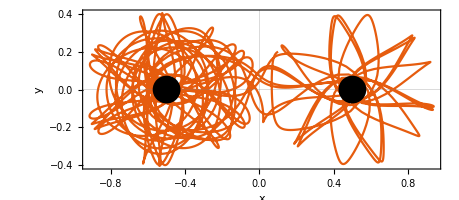

```mathematica
sol=Block[{μ = 0.5, x, y},
NDSolve[
{
x''[t]==2 y'[t]+x[t]-((1-μ) (x[t]+μ))/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ (x[t]-1+μ))/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),
y''[t]==-2 x'[t]+y[t]-((1-μ) y[t])/(((x[t]+μ)^2+y[t]^2)^(3/2))-(μ y[t])/(((x[t]-1+μ)^2+y[t]^2)^(3/2)),

x[0]==0.1,y[0]==0.2,
x'[0]==-0.2,y'[0]==-0.1},
{x,y},{t,0,70}
]
];

Show[
ParametricPlot[{x[t],y[t]} /. sol,{t,0,70},PlotTheme->"Scientific",FrameLabel->{"x","y"},BaseStyle->FontSize->14],
ListPlot[{{-0.5,0},{0.5,0}},PlotStyle->{PointSize[0.05],Black},PlotTheme->"Scientific"]
]
```